# 2D First-Passage time

## Drift towards the equilibrium at (x, xh) = (0, 0) with an absorbing boundary at xh=1. Initial condition is a wide distribution which narrows on approach to the fixed point.

## Write down the nondimensionalized Fokker-Planck equation

```mathematica
FP=λ*D[xh*P[x, xh], x]+D[xh*P[x, xh], xh]-κ*D[x*P[x, xh],xh]+λ*D[P[ x, xh],{x,2}]+D[P[x, xh],{xh,2}]
```

P[x,xh]+xh P^(0,1)[x,xh]-x κ P^(0,1)[x,xh]+P^(0,2)[x,xh]+xh λ P^(1,0)[x,xh]+λ P^(2,0)[x,xh]

## Choose the parameter values

```mathematica
λs = {0.02, 0.045, 0.1, 0.2};
κs = { 0.05,0.1, 0.19, 0.49};
params = Flatten[Table[{λ->l, κ->k}, {l, λs}, {k, κs}], 1]
legend =  Flatten[Table["λ="<>ToString[l]<>"; "<> "κ="<>ToString[k], {l, λs},{k, κs}], 1];
cstar = Flatten[Table[Re[2*κ/(1+Sqrt[1-4*κ*λ])]/.p, {p, params}]]
products = Table[i*j, {i, λs}, {j, κs}]
```

{{λ→0.02,κ→0.05},{λ→0.02,κ→0.1},{λ→0.02,κ→0.19},{λ→0.02,κ→0.49},{λ→0.045,κ→0.05},{λ→0.045,κ→0.1},{λ→0.045,κ→0.19},{λ→0.045,κ→0.49},{λ→0.1,κ→0.05},{λ→0.1,κ→0.1},{λ→0.1,κ→0.19},{λ→0.1,κ→0.49},{λ→0.2,κ→0.05},{λ→0.2,κ→0.1},{λ→0.2,κ→0.19},{λ→0.2,κ→0.49}}

{0.0500501,0.100201,0.190728,0.494898,0.050113,0.100454,0.191653,0.501309,0.0502525,0.101021,0.193754,0.516698,0.0505103,0.102084,0.197827,0.550641}

{{0.001,0.002,0.0038,0.0098},{0.00225,0.0045,0.00855,0.02205},{0.005,0.01,0.019,0.049},{0.01,0.02,0.038,0.098}}

## Set up the mesh, boundary conditions, and initial condition

#### Choose the largest initial width in dimensionful units.

```mathematica
Table[(κ/λ)/.p, {p, params}]
```

{2.5,5.,9.5,24.5,1.11111,2.22222,4.22222,10.8889,0.5,1.,1.9,4.9,0.25,0.5,0.95,2.45}

```mathematica
varCheck =  {{1/(2κ)+((1+κ) λ)/(2κ),1/2},{1/2,(1+κ)/2}}/.params[[13]]
```

{{12.1,1/2},{1/2,0.525}}

```mathematica
varChoice=13;
```

```mathematica
xStds = Table[Sqrt[ 1/(2κ)+((1+κ) λ)/(2κ)]/.params[[varChoice]],Length[params]]
xhStds = N[Table[ Sqrt[(1+κ)/2]/.p, {p, params}]]
```

{3.47851,3.47851,3.47851,3.47851,3.47851,3.47851,3.47851,3.47851,3.47851,3.47851,3.47851,3.47851,3.47851,3.47851,3.47851,3.47851}

{0.724569,0.74162,0.771362,0.863134,0.724569,0.74162,0.771362,0.863134,0.724569,0.74162,0.771362,0.863134,0.724569,0.74162,0.771362,0.863134}

#### Boundary condition at x*=1, y* = 2k/(1+Sqrt(1-4*l*k))

```mathematica
Needs["NDSolve`FEM`"]
```

```mathematica
x0 = 8;
xls=-5*xStds
xrs = x0+5*xStds
xhls=cstar
xhrs = x0+5*xhStds
```

{-17.3925,-17.3925,-17.3925,-17.3925,-17.3925,-17.3925,-17.3925,-17.3925,-17.3925,-17.3925,-17.3925,-17.3925,-17.3925,-17.3925,-17.3925,-17.3925}

{25.3925,25.3925,25.3925,25.3925,25.3925,25.3925,25.3925,25.3925,25.3925,25.3925,25.3925,25.3925,25.3925,25.3925,25.3925,25.3925}

{0.0500501,0.100201,0.190728,0.494898,0.050113,0.100454,0.191653,0.501309,0.0502525,0.101021,0.193754,0.516698,0.0505103,0.102084,0.197827,0.550641}

{11.6228,11.7081,11.8568,12.3157,11.6228,11.7081,11.8568,12.3157,11.6228,11.7081,11.8568,12.3157,11.6228,11.7081,11.8568,12.3157}

```mathematica
icPos = Table[{x0,x0}, {c, cstar}];
icVar = {{1/(2κ)+((1+κ) λ)/(2κ),1/2},{1/2,(1+κ)/2}}/.params[[varChoice]] ;
ic0 = N[Table[PDF[MultinormalDistribution[pos,icVar], {x, xh}], {pos, icPos}]];(*ic0 : Choose widest s.s. distribution of the parameter values*)
(*icSS = N[Table[PDF[MultinormalDistribution[icPos,{{1/(2κ)+((1+κ) λ)/(2κ),1/2},{1/2,(1+κ)/2}}/.p], {x, xh}], {p, params}]];*)
(*icSS : Choose s.s. distribution width for each of the parameter values*)
bcFunc[xl_, xr_, xhl_, xhr_] :={P[xl, xh]==0,
           P[xr, xh]==0,
           P[x, xhr]==0,
           P[x, xhl]==0
}
ΩFunc[xl_, xr_, xhl_, xhr_] :=ImplicitRegion[True,{{x,xl,xr},{xh,xhl,xhr}}];
bcs = MapThread[bcFunc, {xls, xrs, xhrs, xhls}];
minFunc[xStd_, xhStd_]:=Min[6*xStd, 6*xhStd]/300;
cellDistances = MapThread[minFunc, {xStds, xhStds}]
Ω=MapThread[ΩFunc,{xls, xrs, xhls, xhrs}];
```

{0.0144914,0.0148324,0.0154272,0.0172627,0.0144914,0.0148324,0.0154272,0.0172627,0.0144914,0.0148324,0.0154272,0.0172627,0.0144914,0.0148324,0.0154272,0.0172627}

```mathematica
xhCheckFunc[xhl_, c_]:=c≤ xhl
```

```mathematica
MapThread[xhCheckFunc, {x0-4*xhStds, cstar}]
```

{True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True}

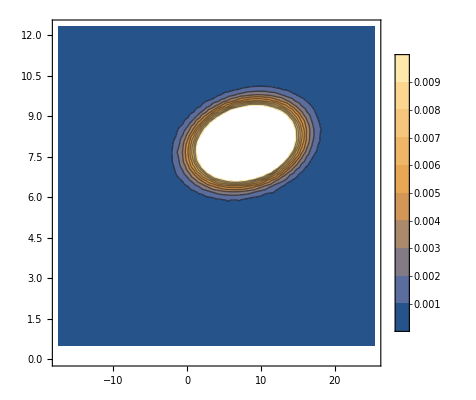

```mathematica
toPlot=4;
ContourPlot[ic0[[toPlot]], {x, xls[[toPlot]], xrs[[toPlot]]}, {xh, xhls[[toPlot]], xhrs[[toPlot]]}, PlotRange->{0, 0.01}, PlotLegends->Automatic]
```

## Calculate the time-integrated probability distribution and the flux through the boundary

```mathematica
NDSolverParams[param_, ic_, bc_, reg_, cell_] :=Module[{N},
N = NDSolve[Join[{(FP/. param)==-ic}, bc],
                                   P,{x, xh}∈reg, 
Method->{"FiniteElement", "MeshOptions"->{"MaxCellMeasure"->cell}}];
Return[(P/.N[[1]])];
]
```

```mathematica
(*solsSS=MapThread[NDSolverParams, {params, icSS, bcs, meshes}];*)
solsIc0=MapThread[NDSolverParams, {params, ic0, bcs, Ω, cellDistances}];
```

```mathematica
solsIc0[[1]]["ElementMesh"]["Wireframe"]
```

-Graphics-

```mathematica
(*fluxSS = Table[Derivative[0,1][sol],{sol, solsSS}];*)
fluxXIc0 = Table[Derivative[0,1][sol],{sol, solsIc0}];
```

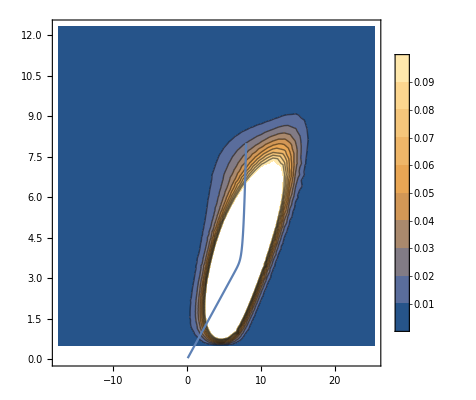

```mathematica
toShow = 8;cIc0 =ContourPlot[solsIc0[[toShow]][x, xh], {x, xls[[toShow]], xrs[[toShow]]}, {xh, xhls[[toShow]], xhrs[[toShow]]}, PlotLegends->Automatic, PlotRange->{0, 0.1}];
pa = ParametricPlot[{ⅇ^(-t/2) (x0 Cosh[1/2 t √(1-4 κ λ)]+((x0-2 x0*λ) Sinh[1/2 t √(1-4 κ λ)])/(√(1-4 κ λ))),ⅇ^(-t/2) (x0* Cosh[1/2 t √(1-4 κ λ)]+((-x0+2 x0* κ) Sinh[1/2 t √(1-4 κ λ)])/(√(1-4 κ λ)))}/.params[[toShow]], {t, 0, 200}, PlotRange->10];
(*Show[cSS]*)
Show[{cIc0, pa}]
```

```mathematica
XIc0 =MapThread[#1[x,#2]&,{fluxXIc0,cstar}];
```

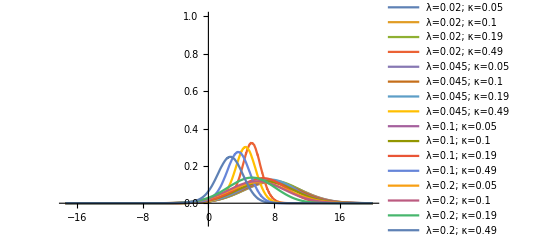

```mathematica
Plot[XIc0, {x, -20, 20}, PlotRange->{-0.1, 1}, PlotLegends->legend]
```

```mathematica
(*normsSS = Table[NIntegrate[xp, {x, -10, 15}, WorkingPrecision->10], {xp, XSS}]
meansSS= Table[NIntegrate[xp*x, {x, -10, 15}, WorkingPrecision->10], {xp, XSS}]
secondSS = Table[NIntegrate[xp*x*x, {x, -10, 15}, WorkingPrecision->10], {xp, XSS}];
varsSS= secondSS-meansSS^2
diffSS = varsSS/meansSS;*)
```

```mathematica
IntegFunc[f_, l_, r_] := NIntegrate[f, {x, l, r}, WorkingPrecision->10]
```

```mathematica
normsIc0 = MapThread[IntegFunc, {XIc0, xls, xrs}]
meansIc0= MapThread[IntegFunc, {XIc0*x, xls, xrs}]
secondIc0 = MapThread[IntegFunc, {XIc0*x*x, xls, xrs}]
varsIc0 = secondIc0-meansIc0^2
diffIc0 = varsIc0/meansIc0;
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {4.833994826}. NIntegrate obtained 0.9969698057 and 0.0004672645083 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {3.831220117}. NIntegrate obtained 0.998609208 and 0.0001846101373 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {3.246268203}. NIntegrate obtained 1.000072743 and 0.0002253292496 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

{1.002364429,1.002081961,1.000237989,0.9969698057,1.00227461,1.002123065,1.000496275,0.998609208,1.002415584,1.002225216,1.000936942,1.000072743,1.002550412,1.002405103,1.001672054,1.00071695}

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {7.424496158}. NIntegrate obtained 4.940197826 and 0.002772353503 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {7.424496158}. NIntegrate obtained 4.316787438 and 0.001261190523 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {5.41894674}. NIntegrate obtained 3.513330667 and 0.0007858865876 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

{7.832718696,7.788001222,7.552929686,4.940197826,7.601601029,7.512014752,7.115661086,4.316787438,7.101891885,6.926574718,6.318912513,3.513330667,6.210389684,5.925487836,5.146615181,2.579399274}

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {7.424496158}. NIntegrate obtained 26.98542854 and 0.01766478157 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {6.003898654}. NIntegrate obtained 21.06607256 and 0.01005531633 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {6.421721449}. NIntegrate obtained 14.87287334 and 0.00483320602 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

{73.35201686,72.49121915,67.57276959,26.98542854,69.8317602,68.1233628,60.32269562,21.06607256,62.60756143,59.49176263,48.84580628,14.87287334,51.09650733,46.60877905,35.07521683,9.502276458}

{12.000535,11.838256,10.526023,2.579874,12.047422,11.692997,9.6900629,2.4314188,12.170693,11.514325,8.9171509,2.529381,12.527567,11.497373,8.587569,2.84897584}

```mathematica
grid = Flatten[Table[{l, s}, {l, λs}, {s, κs}], 1];
params
```

{{λ→0.02,κ→0.05},{λ→0.02,κ→0.1},{λ→0.02,κ→0.19},{λ→0.02,κ→0.49},{λ→0.045,κ→0.05},{λ→0.045,κ→0.1},{λ→0.045,κ→0.19},{λ→0.045,κ→0.49},{λ→0.1,κ→0.05},{λ→0.1,κ→0.1},{λ→0.1,κ→0.19},{λ→0.1,κ→0.49},{λ→0.2,κ→0.05},{λ→0.2,κ→0.1},{λ→0.2,κ→0.19},{λ→0.2,κ→0.49}}

```mathematica
(*normArraySS = ArrayReshape[normsSS, {5, 5}];
varArraySS = ArrayReshape[varsSS, {5, 5}];
meanArraySS = ArrayReshape[meansSS, {5, 5}];
diffArraySS = ArrayReshape[diffSS, {5, 5}];*)
normArrayIc0 = ArrayReshape[normsIc0, {4,4}];
varArrayIc0 = ArrayReshape[varsIc0, {4,4}];
meanArrayIc0 = ArrayReshape[meansIc0, {4,4}];
diffArrayIc0 = ArrayReshape[diffIc0, {4,4}];
```

```mathematica
cf[x_]:=Blend[{{-2, Red},{ 1,White},{5,Blue}}, x]
```

```mathematica
xticks = Transpose[{{1, 2, 3, 4}, λs}];
yticks = Transpose[{{1, 2, 3, 4}, κs}];
```

```mathematica
ArrayPlot[varArrayIc0, ColorFunction->(Blend[{{-1, Red},{ 0,White},{1,Blue}},#]&), PlotLegends->{Placed[BarLegend[Automatic,None,LegendLabel->"var(x)"],Right]}, FrameTicks->{xticks, yticks}, DataReversed->True, FrameLabel->{λ, κ}]

ArrayPlot[ArrayReshape[Table[Blend[{{-2, Red},{ 0,White},{5,Blue}}, i],{i,Flatten[meanArrayIc0]}], {4,4}], PlotLegends->{Placed[BarLegend[{cf[#]&,{-2, 5}},LegendLabel->"mean(x)"],Right]}, FrameTicks->{xticks, yticks}, DataReversed->True, FrameLabel->{λ, κ}]

ArrayPlot[normArrayIc0, ColorFunction->(Blend[{White,Blue},#]&), PlotLegends->{Placed[BarLegend[Automatic,Automatic,LegendLabel->"norm(e(x))"],Right]}, FrameTicks->{xticks, yticks}, DataReversed->True, FrameLabel->{λ, κ}]
```

-Graphics-

-Graphics-

-Graphics-

```mathematica
A3= {{ 0,λ},{-κ, 1}}/. {λ->0.2,κ->4.9}
B3 = {{Sqrt[λ],0},{0,1 }}/.  {λ->0.2,κ->4.9}
s0 = {{1/(2κ)+((1+κ) λ)/(2κ),1/2},{1/2,(1+κ)/2}}/.params[[13]]
```

{{0,0.2},{-4.9,1}}

{{0.447214,0},{0,1}}

{{1.3,1/2},{1/2,0.75}}

```mathematica
S[t_] = FullSimplify[MatrixExp[A3].s0.MatrixExp[Transpose[A3]]+Integrate[MatrixExp[-Integrate[A3, {s, tp, t}]].B3.Transpose[B3].MatrixExp[-Integrate[Transpose[A3], {s, tp, t}]], {tp, 0, t}]]
```

{{(0.553155-7.96076×10^-18 ⅈ)+ⅇ^(-1. t) ((-0.161644+6.09102×10^-18 ⅈ)-(0.0608051-1.86974×10^-18 ⅈ) Cos[1.7088 t]-(0.0131373-4.65868×10^-18 ⅈ) Sin[1.7088 t]),(-3.11232-1.46509×10^-16 ⅈ)+ⅇ^(-1. t) ((-0.40411+1.02883×10^-16 ⅈ)-(0.0958904-4.3626×10^-17 ⅈ) Cos[1.7088 t]-(0.292603-3.3761×10^-17 ⅈ) Sin[1.7088 t])},{(-3.11232-3.91934×10^-18 ⅈ)+ⅇ^(-1. t) ((-0.40411+3.86223×10^-17 ⅈ)-(0.0958904+3.47029×10^-17 ⅈ) Cos[1.7088 t]-(0.292603-3.80276×10^-17 ⅈ) Sin[1.7088 t]),(58.6064-4.54614×10^-16 ⅈ)+ⅇ^(-1. t) ((-3.96027+6.17042×10^-16 ⅈ)+(1.01027-1.62427×10^-16 ⅈ) Cos[1.7088 t]-(1.14115-2.33557×10^-16 ⅈ) Sin[1.7088 t])}}

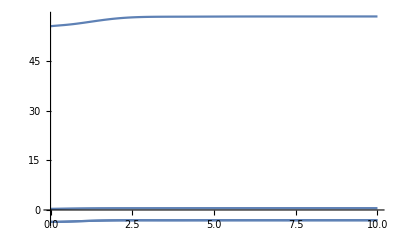

```mathematica
Plot[Re[S[t]], {t, 0, 10}]
```

```mathematica
Re[0.5+0.5*I]
```

0.5